# Mathematica Cheat Sheet

## Symbols to copy-paste and shortcuts

```mathematica
≤ ≥ -> ∈
```

∈ sign is escape, e, l, escape

## Plot

Plot[function, {variable, min, max}, PlotRange → {{xmin, xmax},{ymin, ymax}}, PlotTheme → “Something]

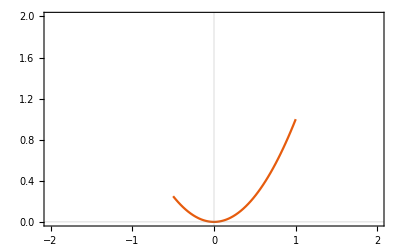

```mathematica
Plot[x^2, {x,-0.5,1},PlotRange->{{-2,2},{0,2}}, PlotTheme->"Scientific"]
```

### Contour Plot for Implicit equations

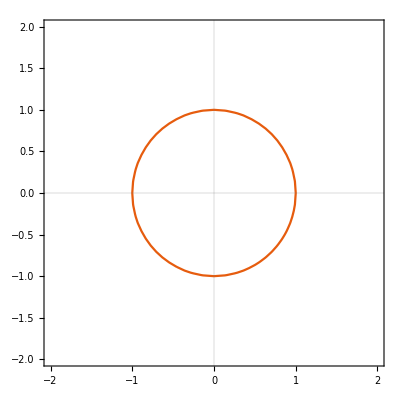

```mathematica
ContourPlot[x^2+y^2 - 1 == 0,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]
```

### Parametric Plot for Parametric Equations

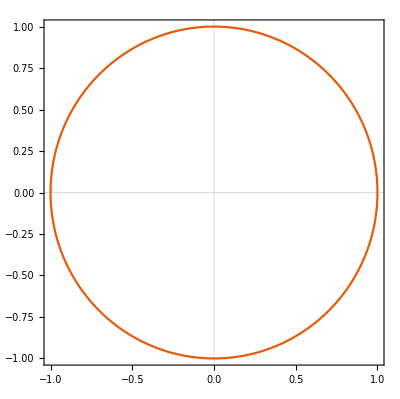

```mathematica
ParametricPlot[{Cos[u],Sin[u]},{u,0,2*Pi},PlotTheme->"Scientific"]
```

### Plotting Data

{{0,1},{1,0},{3,2},{5,4}}

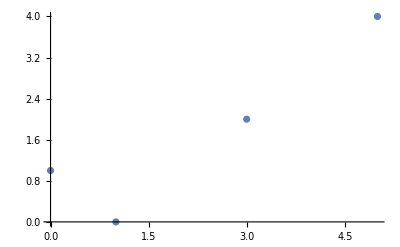

```mathematica
data = {{0,1},{1,0},{3,2},{5,4}}
ListPlot[data]
```

### Plot 3D

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2},PlotTheme->"Scientific"]
```

-Graphics3D-

### ContourPlot3D for 3D curves defined implicitly

```mathematica
ContourPlot3D[x^2 + y^2 + z^2 - 1 == 0, {x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"]
```

-Graphics3D-

ParametricPlot3D for 3D curves defined parametrically

```mathematica
ParametricPlot3D[{Sin[u]*Cos[v],Sin[u]*Sin[v],Cos[u]},{u,0,Pi},{v,0,2*Pi},PlotTheme->"Scientific"]
```

-Graphics3D-

### Region Plot (for Calculus)

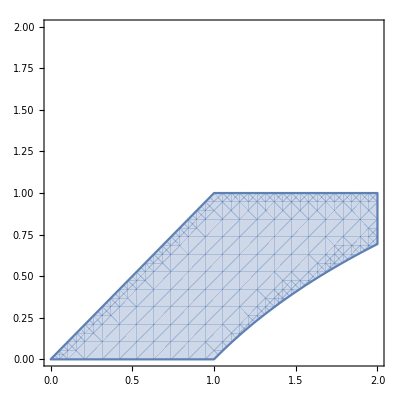

```mathematica
RegionPlot[ 0<y<1&&y<x<Exp[y],{x,0,2},{y,0,2}]
```

### RegionPlot 3D

```mathematica
RegionPlot3D[x^2+y^3-z^2>0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

### Implicit Region (also Calculus)

ImplicitRegion[-1<y<1&&-1<x<y^2&&-1≤x≤1&&0≤y≤2,{x,y}]

ImplicitRegion[1<y<1+x^2&&-1<x<1&&-1≤x≤1&&0≤y≤2,{x,y}]

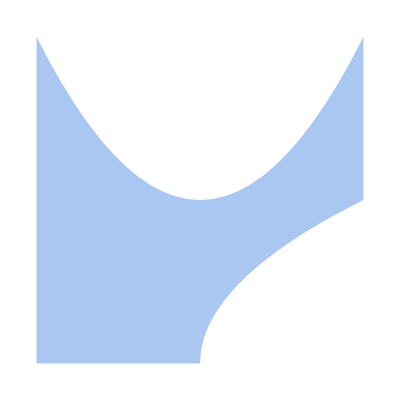

```mathematica
R=ImplicitRegion[-1<y<1 && -1<x<y^2,{{x,-1,1},{y,0,2}}]
T=ImplicitRegion[1<y<1+x^2 && -1<x<1,{{x,-1,1},{y,0,2}}]
Show[Region[R], Region[T]]
```

### Fancy Arguments for Plot

```mathematica
PlotTheme->"Scientific",PlotLegends->Automatic, Contours->{1,4,9}
Axes->True, AxesLabel->{z,y}
```

## Manipulate

```mathematica
Manipulate[Plot[m*x+b, {x,-10,10},PlotRange->{{-10,10},{-4,4}}, PlotTheme->"Scientific"],{m,-5,5,Appearance->"Labeled"},{b,-4,4,Appearance->"Labeled"}]
```

## Solve

```mathematica
Solve[A*Exp[k*t]==2*A,t,Reals]
```

{{t→Log[2]/k}}

### Solve 2 equations for an intersection

```mathematica
Clear[A,B]
N[Solve[(x^2)/(3^2)+(y^2)/(5^2)-1==0&&y==4*x+7,{x,y}]]
```

{{x→-2.46341,y→-2.85365},{x→-0.518836,y→4.92466}}

### Gensolve

```mathematica
gensol = Solve[A*Exp[k*t]==2*A,t, Reals]
specsol=gensol/.{k->1/100}
N[specsol]
```

{{t→Log[2]/k}}

{{t→100 Log[2]}}

{{t→69.3147}}

### Limit

```mathematica
Limit[Exp[k*t],t->∞]
```

ConditionalExpression[∞,k>0]

### Finding Best Fit for data

The numbers in params after m and b are estimates. You can get those estimates by using manipulate to get the values so that the line looks close.

b+m t

{m→0.694915,b→0.186441}

0.186441+0.694915 t

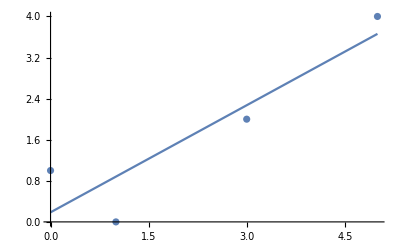

```mathematica
line = m*t+b
params = FindFit[data,line,{{m,0.7},{b,0.2}},t]
bestline = line/.params
Show[ListPlot[data],Plot[bestline,{t,0,5},PlotRange->{{0,5},{0,5}}]]
```

## Calculus

### Differentiation

```mathematica
D[x^n, x]
```

n x^(-1+n)

### Integration

```mathematica
Integrate[x^n, x]
```

x^(1+n)/(1+n)

### Region Plot

```mathematica
RegionPlot[ 0<y<1&&y<x<Exp[y],{x,0,2},{y,0,2}]
```

-Graphics-

## General Tricks

### Clear

If you are getting an actual number when you expected to have a general solution, you may have defined some variables that you are using elsewhere in the notebook. Since all Mathematica variables are global, you need to use clear to make them not assigned any more.

```mathematica
Clear[m,b]
```

```mathematica
ClearAll
```

### Get output of last cell (can put it anywhere in an equation)

```mathematica
%
```

### Get numerical Value

```mathematica
N[%]
```

### Simplify

```mathematica
Simplify[%]
```

### Show

Put this function around multiple plot functions to get them both to show up on the same graph

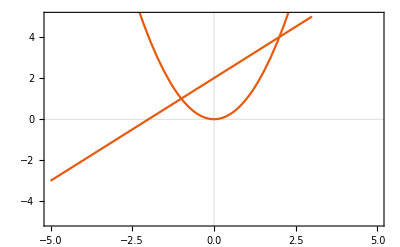

```mathematica
Show[Plot[x+2, {x,-5,5},PlotRange->{{-5,5},{-5,5}}, PlotTheme->"Scientific"], Plot[x^2, {x,-5,5},PlotRange->{{-5,5},{5,5}}, PlotTheme->"Scientific"]]
```

### Still Confused About a Function?

Put a question mark (?) in front of any function to get some documentation from Mathematica

```mathematica
?Clear
```

Clear[symbol_1,symbol_2,…] clears values and definitions for the symbol_i. 
Clear[form,form,…] clears values and definitions for all symbols whose names match any of the string patterns form_i.